# Independent Project Codes

## Estimation of Larmor frequency from Spin-Locking Experiment

### Defining Model

```mathematica
ClearAll["Global`*"]
ω[Δω_,ωR_]:=Sqrt[Δω^2+ωR^2];
θ[Δω_,ωR_]:= ArcCos[ωR/ω[Δω,ωR]];
My[Δω_,ωR_,t_,T2_]:= Cos[θ[Δω,ωR]] (Cos[θ[Δω,ωR]]) + ((Sin[θ[Δω,ωR]])^2)*Cos[ω[Δω,ωR] t]*Exp[-t/T2];
```

### Simulating Experimental data

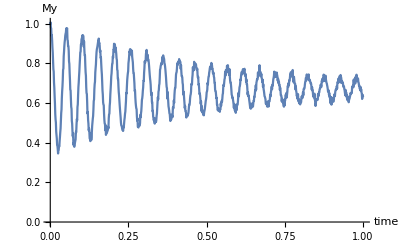

```mathematica
Δω0 = 70;
ωR = 100;
T2 = 0.5;
dt = 0.001;
T = Table[t,{t,0,1,dt}];
noise = RandomVariate[NormalDistribution[0, 0.01], Length[T]];
data1 = Table[{t,My[Δω0,ωR,t,T2]+noise[[1+t/dt]]},{t,0,1,0.001}];
(*Simulating FID*)
ListLinePlot[data1,PlotRange->All,AxesLabel->{"time","My"}]
```

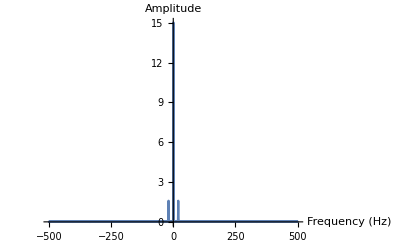

```mathematica
(* Fourier transform of the FID*)
n = Length[data1];
data2fid = Table[data1[[i]][[2]],{i,1,n}];
spec2fm= RotateLeft[Fourier[Join[data2fid,Table[0,{n,1,n}]]],n];
νN = 0.5/dt;
spec2fsim = Table[{(i-n)νN/n,spec2fm[[i]]},{i,1,Length[spec2fm]}];
ListLinePlot[Re[spec2fsim],{PlotRange->All},AxesLabel->{"Frequency (Hz)","Amplitude"}]
```

## Sequential Monte Carlo Bayesian Inference

```mathematica
(* Functions for calculating mean and covariance*)
MEAN[X_,Ω_]:= Sum[X[[i]] Ω[[i]],{i,1,Length[Ω]}];
COV[X_,Ω_]:= Sum[Ω[[i]](X[[i]])^2,{i,1,Length[Ω]}]-(MEAN[X,Ω])^2 ;

(*Likelihood of the data*)
Q[data_,x_]:= Sum[(data[[i]][[2]]- My[x,ωR,T[[i]],T2])^2,{i,1,Length[data]}];
PLIKELIHOOD[data_,x_] := Exp[-Q[data,x]/(2)];

(*Resampling*)
ResamplePDF[a_,X_,Ω_,x_]:= Sum[Ω[[i]]Exp[(x-ResampleMean[a,X,Ω][[i]])^2/(2ResampleCOV[a,X,Ω])]/Sqrt[2π ResampleCOV[a,X,Ω]],{i,1,Length[Ω]}];
ResampleMean[a_,xj_,X_,Ω_]:=a xj + (1-a)MEAN[X,Ω]
ResampleCOV[a_,X_,Ω_]:= ((1-a)^2)COV[X,Ω];
RESAMPLE[Xnew_,σ_,Ω_,X_,a_]:=Do[xj=RandomChoice[Ω->X,1];
                                                            μi= ResampleMean[a,xj,X,Ω];
                                                            xi= RandomVariate[NormalDistribution[μi,σ],1];
                                                            AppendTo[Xnew,xi],{i,1,Length[Ω]}];
SampleSize[Ω_]:= 1/Sum[(Ω[[i]])^2,{i,1,Length[Ω]}];


SetAttributes[RESAMPLE,HoldFirst]
SetAttributes[UPDATE,HoldFirst]
SetAttributes[IMPLEMENT,HoldAll]
SetAttributes[NORMALIZE,HoldFirst]

(*SMC Update*)
UPDATE[Ω_,P_]:= Do[Ω[[i]]=P[[i]]*Ω[[i]], {i,1,Length[Ω]}];
S[Ω_]:=Sum[Ω[[i]],{i,1,Length[Ω]}];
NORMALIZE[Ω_,S_]:= Do[Ω[[i]]= Ω[[i]]/S,{i,1,Length[Ω]}]; 

IMPLEMENT[data_,Ω_,X_,a_,resampthreshold_,Meanlist_,N_]:= Module[{P,Xnew,σ,sum},
                                                                                                                      P = Table[PLIKELIHOOD[data,X[[i]]],{i,1,Length[X]}];
                                                                                                                       Do[UPDATE[Ω,P];
                                                                                                                            sum = S[Ω];
                                                                                                                            NORMALIZE[Ω,sum];
                                                                                                                            AppendTo[Meanlist,MEAN[X,Ω]];
                                                                                                                            Xnew={};
                                                                                                                             σ=ResampleCOV[a,X,Ω];
                                                                                                                             If[SampleSize[Ω]<resampthreshold,RESAMPLE[Xnew,σ,Ω,X,a];Ω=Table[1/Length[X],{i,1,Length[X]}];P=Table[PLIKELIHOOD[data,Xnew[[i]]],{i,1,Length[X]}];,Xnew=X;];
                                                                                                                              X=Xnew;
                                                                                                                               ,{i,1,N}]]
```

#### Uniform Prior

```mathematica
ω1 = 30;
ω2 = 150;
np = 2000;
Prior =UniformDistribution[{ω1,ω2}];
X = RandomVariate[Prior,np];
Ω = Table[1/np,{i,1,np}];
a=0.98;
resampthreshold=0.6;
Meanlist={MEAN[X,Ω ]};
IMPLEMENT[data1,Ω,X,a,resampthreshold,Meanlist,20]
```

General::munfl: 5.27187×10^-45 1.30946×10^-267 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.0475×10^-44 8.05791×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.32058×10^-45 3.88908×10^-267 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
AbsolutePercentError=Abs[(Meanlist[[-1]]-Δω0)/Δω0]*100
```

0.020173

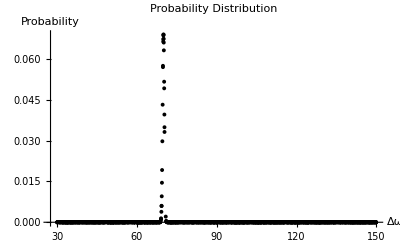

```mathematica
data2 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data2,PlotStyle->{PointSize[0.007],Darker[Black]},PlotRange->All,PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

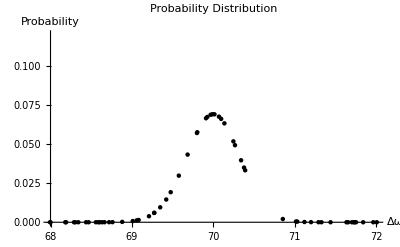

```mathematica
data4 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data4,PlotRange->{{68,72},{0,0.12}},PlotStyle->{PointSize[0.008],Darker[Black]},PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

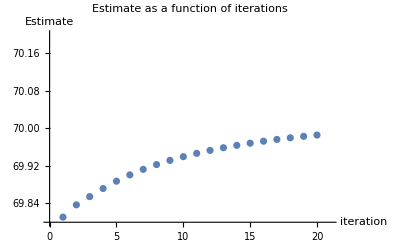

```mathematica
data3 = Table[{i-1,Meanlist[[i]]},{i,1,Length[Meanlist]}];
ListPlot[data3,PlotRange->{{0,21},{69.8,70.2}},PlotLabel->"Estimate as a function of iterations",AxesLabel->{"iteration","Estimate"}]
```

```mathematica
Meanlist[[-1]]
```

69.9859

#### Flat Gaussian Prior

```mathematica
ω1 = 30;
ω2 = 150;
np = 2000;
Prior = NormalDistribution[(ω1+ω2)/2,(ω2-ω1)/3];
X = RandomVariate[Prior,np];
Ω = Table[1/np,{i,1,np}];
a=0.98;
resampthreshold=0.6;
Meanlist={};
IMPLEMENT[data1,Ω,X,a,resampthreshold,Meanlist,20]
```

General::munfl: 3.38903×10^-87 1.19983×10^-261 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.99511×10^-65 4.76668×10^-259 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.3855×10^-65 1.09786×10^-258 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
AbsolutePercentError=Abs[(Meanlist[[-1]]-Δω0)/Δω0]*100
```

0.0443501

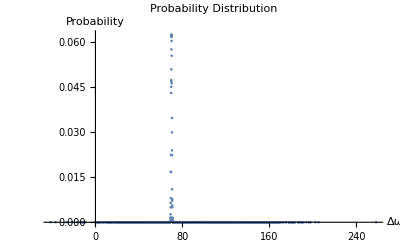

```mathematica
data2 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data2,PlotRange->All,PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

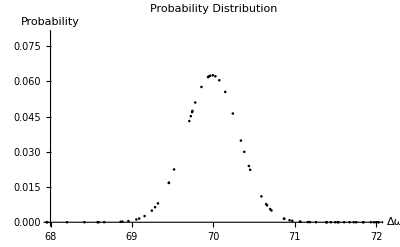

```mathematica
data4 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data4,PlotRange->{{68,72},{0,0.08}},PlotStyle->{Black},PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

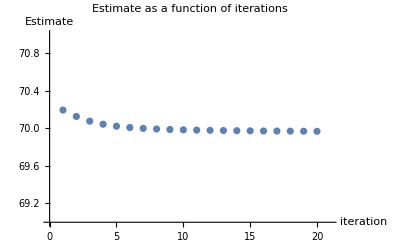

```mathematica
data3 = Table[{i,Meanlist[[i]]},{i,1,Length[Meanlist]}];
ListPlot[data3,PlotRange->{{0,21},{69,71}},PlotLabel->"Estimate as a function of iterations",AxesLabel->{"iteration","Estimate"}]
```

## Estimation of Dipolar coupling strength in Gypsum

## Simulations

### 2-spin simulation

#### With Only Strong Coupling

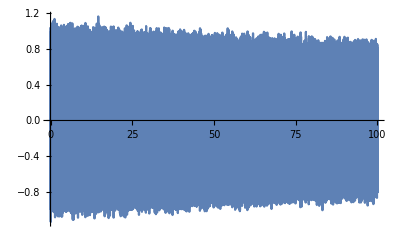

```mathematica
h12 =2 KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]- KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]-KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
h4= KroneckerProduct[PauliMatrix[1],PauliMatrix[0]] +  KroneckerProduct[PauliMatrix[0],PauliMatrix[1]];
h5 =  KroneckerProduct[PauliMatrix[2],PauliMatrix[3]] +  KroneckerProduct[PauliMatrix[3],PauliMatrix[2]];

HS[ωs_]:=ωs h12/4;
U[ωs_,t_]:= MatrixExp[-I HS[ωs]t];
evolve[ρ_,t_,ωs_]:= U[ωs,t].ρ.ConjugateTranspose[U[ωs,t]]
Mx[ρ_]:= Tr[(h4+I h5).ρ]/4

(*defining constants*)
ωs= 92.9911425;          (*units of radians/ms*)
T2 = 500;                          (*units of ms*)
dt = 0.005;
T = Table[t,{t,0,100,dt}];            (*units of ms*)

data1 = Table[{t,Exp[-t/T2]Mx[evolve[h4,t,ωs]]+RandomVariate[NormalDistribution[0,0.1]]},{t,0,100,dt}];
data2= Table[{T[[i]],Re[data1[[i]][[2]]]/2},{i,1,Length[data1]}];
ListLinePlot[data2]
```

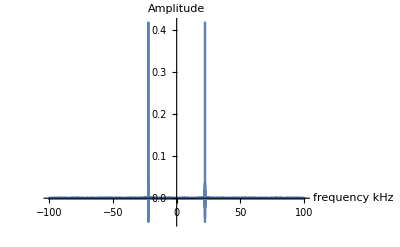

```mathematica
n=Length[data1];
data2fid = Table[Re[data1[[i]][[2]]],{i,1,Length[data1]}];
spec2fm= RotateLeft[Fourier[Join[data2fid,Table[0,{n,1,Length[data1]}]],FourierParameters->{-1, 1}],Length[data1]];
νN = 0.5/dt;
spec2fsim = Table[{(i-(n+1))*νN/n,spec2fm[[i]]},{i,1,Length[spec2fm]}];
ListLinePlot[Re[spec2fsim],{PlotRange->All},AxesLabel->{"frequency kHz","Amplitude"}]
```

## 4-spin simulation

```mathematica
ClearAll["Global`*"]
```

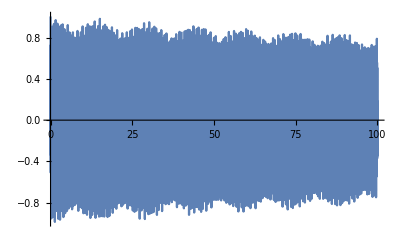

```mathematica
h12 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[3],PauliMatrix[3]],PauliMatrix[0]],PauliMatrix[0]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[1],PauliMatrix[1]],PauliMatrix[0]],PauliMatrix[0]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[2],PauliMatrix[2]],PauliMatrix[0]],PauliMatrix[0]];

h14 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[3],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[3]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[1],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[1]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[2],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[2]];

h24 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[3]],PauliMatrix[0]],PauliMatrix[3]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[1]],PauliMatrix[0]],PauliMatrix[1]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[2]],PauliMatrix[0]],PauliMatrix[2]];

h13 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[3],PauliMatrix[0]],PauliMatrix[3]],PauliMatrix[0]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[1],PauliMatrix[0]],PauliMatrix[1]],PauliMatrix[0]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[2],PauliMatrix[0]],PauliMatrix[2]],PauliMatrix[0]];

h23 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[3]],PauliMatrix[3]],PauliMatrix[0]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[1]],PauliMatrix[1]],PauliMatrix[0]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[2]],PauliMatrix[2]],PauliMatrix[0]];

h34 = 2 KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[3]],PauliMatrix[3]]-  KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[2]],PauliMatrix[2]]- KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[1]],PauliMatrix[1]];

h4 = KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[1],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[0]]+KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[1]],PauliMatrix[0]],PauliMatrix[0]]+KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[1]],PauliMatrix[0]]+KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[1]];

h5= KroneckerProduct[KroneckerProduct[KroneckerProduct[PauliMatrix[0],PauliMatrix[0]],PauliMatrix[0]],PauliMatrix[0]];

HD[ωs_,ωw_]:=ωs (h12+h34)/4 + ωw(h13+h23+h14+h24)/4;
U[ωs_,ωw_,t_]:= MatrixExp[-I HD[ωs,ωw]t];
evolve[ρ_,t_,ωs_,ωw_]:= U[ωs,ωw,t].ρ.ConjugateTranspose[U[ωs,ωw,t]]
Mx[ρ_]:= Tr[h4.ρ]/4

dt = 0.005;
data1= Table[{t,Exp[-t/T2]Mx[evolve[h4,t,ωs,ωw]]/16+ RandomVariate[NormalDistribution[0,0.01],1][[1]]},{t,0,100,dt}];
ListLinePlot[data1,PlotRange->All]
```

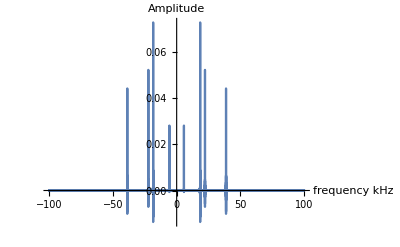

```mathematica
n=Length[data1];
data2fid = Table[Re[data1[[i]][[2]]],{i,1,Length[data1]}];
spec2fm= RotateLeft[Fourier[Join[data2fid,Table[0,{n,1,Length[data1]}]],FourierParameters->{-1, 1}],Length[data1]];
νN = 0.5/dt;
spec2fsim = Table[{(i-(n+1))*νN/n,spec2fm[[i]]},{i,1,Length[spec2fm]}];
ListLinePlot[Re[spec2fsim],{PlotRange->All},AxesLabel->{"frequency kHz","Amplitude"}]
```

### With AM RF Pulse

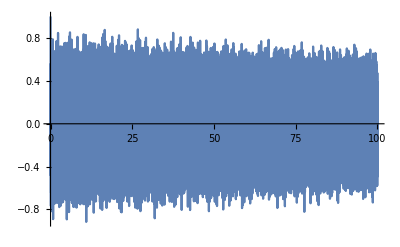

```mathematica
(*Numerical simulation for time dependent Hamiltonian*)
HT[ωs_,ωw_,ω1_,ωm_,t_]:= HD[ωs,ωw] + ω1 Cos[ωm t]h4/2;
Uk[ωs_,ωw_,ω1_,ωm_,k_,dt_]:= MatrixExp[-I HT[ωs,ωw,ω1,ωm,k dt] dt];
SetAttributes[Unitary,HoldFirst]
Unitary[Ulist_,ωs_,ωw_,ω1_,ωm_,T_,dt_]:=Do[
                                                                                                           UKminus1= Ulist[[k]];
                                                                                                                UKminus1=Uk[ωs,ωw,ω1,ωm,k,dt].UKminus1;
                                                                                                                  AppendTo[Ulist,UKminus1];
                                                                                                                 ,{k,1,Ceiling[T[[-1]]/dt]-1}];
evolveAM[Ulist_]:= Table[Ulist[[i]].h4.ConjugateTranspose[Ulist[[i]]],{i,1,Length[Ulist]}];


ωs= 92.9911425;          (*units of radians/ms*)
T2 = 500; 
ωw = 34.5575192;
dt = 0.005;
T = Table[t,{t,0,100,dt}];            (*units of ms*)
ω1 = 3ωs/4;
ωm =  3ωs/2;
Ulist = {h5};
Unitary[Ulist,ωs,ωw,ω1,ωm,T,dt]
ρlist = evolveAM[Ulist];

data1 = Table[{(j-1)dt,Exp[-(j-1)dt/T2]Mx[ρlist[[j]]]/16+RandomVariate[NormalDistribution[0,0.01]]},{j,1,Length[ρlist]}];
ListLinePlot[data1,PlotRange->All]
```

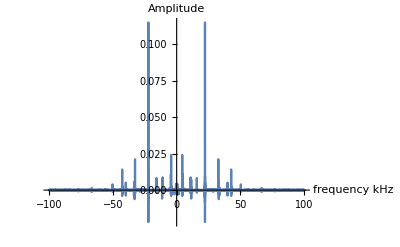

```mathematica
n=Length[data1];
data2fid = Table[Re[data1[[i]][[2]]],{i,1,Length[data1]}];
spec2fm= RotateLeft[Fourier[Join[data2fid,Table[0,{n,1,Length[data1]}]],FourierParameters->{-1, 1}],Length[data1]];
νN = 0.5/dt;
spec2fsim = Table[{(i-(n+1))*νN/n,spec2fm[[i]]},{i,1,Length[spec2fm]}];
ListLinePlot[Re[spec2fsim],{PlotRange->All},AxesLabel->{"frequency kHz","Amplitude"}]
```

## Simulation for Experimental data

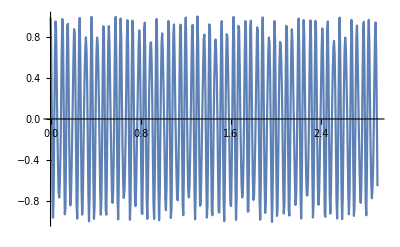

```mathematica
ClearAll["Global`*"]
h12 =2 KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]- KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]-KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
h4= KroneckerProduct[PauliMatrix[1],PauliMatrix[0]] +  KroneckerProduct[PauliMatrix[0],PauliMatrix[1]];
h5 =  KroneckerProduct[PauliMatrix[2],PauliMatrix[3]] +  KroneckerProduct[PauliMatrix[3],PauliMatrix[2]];
h6 = KroneckerProduct[PauliMatrix[0],PauliMatrix[0]];

HS[ωs_,ω1_,ωm_,t_]:=ωs h12/4 + ω1 (Cos[ωm t])h4/2 ;
Uk[ωs_,ω1_,ωm_,k_,t_]:= MatrixExp[-I HS[ωs,ω1,ωm,k t]t];
SetAttributes[Unitary,HoldFirst]
Unitary[Ulist_,ωs_,ω1_,ωm_,T_,dt_]:=Do[Do[
                                                                                                           UKminus1= Ulist[[k]];
                                                                                                                UKminus1=Uk[ωs,ω1,ωm,k,dt].UKminus1;
                                                                                                                  AppendTo[Ulist,UKminus1];
                                                                                                                 ,{k,1,Ceiling[T[[-1]]/dt]}];
Return[Ulist];,{i,1,1}];
evolveAM[Ulist_]:= Table[Ulist[[i]].h4.ConjugateTranspose[Ulist[[i]]],{i,1,Length[Ulist]}];
ρList[ωs_,ω1_,ωm_,T_,dt_]:= Module[{Ulist={h6}}, U=Unitary[Ulist,ωs,ω1,ωm,T,dt];
                                                                                                                      Return[evolveAM[U]];];
Mx[ρ_]:= Tr[h4.ρ]/8

ωs =92.9911425;
dt = 0.0055;
ω1 =  50;
ωm =  120;
T2 = 500;
Ulist = {h6};
T = Table[t,{t,0,2.9,dt}];            (*units of ms*)
Unitary[Ulist,ωs,ω1,ωm,T,dt];
ρlist = evolveAM[Ulist];

data1 = Table[{(j-1)dt,Exp[-(j-1)dt/T2]Mx[ρList[ωs,ω1,ωm,T,dt][[j]]]+RandomVariate[NormalDistribution[0,0.01]]},{j,1,Length[T]}];
ListLinePlot[data1,PlotRange->All]
```

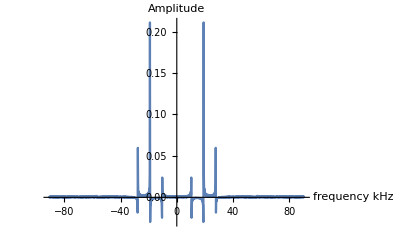

```mathematica
n=Length[data1];
data2fid = Table[Re[data1[[i]][[2]]],{i,1,Length[data1]}];
spec2fm= RotateLeft[Fourier[Join[data2fid,Table[0,{n,1,Length[data1]}]],FourierParameters->{-1, 1}],Length[data1]];
νN = 0.5/dt;
spec2fsim = Table[{(i-(n+1))*νN/n,spec2fm[[i]]},{i,1,Length[spec2fm]}];
ListLinePlot[Re[spec2fsim],{PlotRange->All},AxesLabel->{"frequency kHz","Amplitude"}]
```

## Sequential Monte Carlo Bayesian Inference

```mathematica
(* Functions for calculating mean and covariance*)
MEAN[X_,Ω_]:= Sum[X[[i]] Ω[[i]],{i,1,Length[Ω]}];
COV[X_,Ω_]:= Sum[Ω[[i]](X[[i]])^2 ,{i,1,Length[Ω]}]-(MEAN[X,Ω])^2;

(*Likelihood of the data*)
Q[data_,ρ_]:= Sum[(data[[i]][[2]]-Exp[-(i-1)dt/T2]Mx[ρ[[i]]])^2,{i,1,Length[data]}];
PLIKELIHOOD[data_,ρ_] := Exp[-Q[data,ρ]/(2)];

(*Resampling*)
ResamplePDF[a_,X_,Ω_,x_]:= Sum[Ω[[i]]Exp[(x-ResampleMean[a,X,Ω][[i]])^2/(2ResampleCOV[a,X,Ω])]/Sqrt[2π ResampleCOV[a,X,Ω]],{i,1,Length[Ω]}];
ResampleMean[a_,xj_,X_,Ω_]:=a xj + (1-a)MEAN[X,Ω]
ResampleCOV[a_,X_,Ω_]:= ((1-a)^2)COV[X,Ω];
RESAMPLE[Xnew_,σ_,Ω_,X_,a_]:=Do[xj=RandomChoice[Ω->X,1];
                                                            μi= ResampleMean[a,xj,X,Ω];
                                                            xi= RandomVariate[NormalDistribution[μi,σ],1];
                                                            AppendTo[Xnew,xi],{i,1,Length[Ω]}];
SampleSize[Ω_]:= Re[1/Sum[(Ω[[i]])^2,{i,1,Length[Ω]}]];


SetAttributes[RESAMPLE,HoldFirst]
SetAttributes[UPDATE,HoldFirst]
SetAttributes[IMPLEMENT,HoldAll]
SetAttributes[NORMALIZE,HoldFirst]

(*SMC Update*)
UPDATE[Ω_,P_]:= Do[Ω[[i]]=P[[i]]*Ω[[i]], {i,1,Length[Ω]}];
S[Ω_]:=Sum[Ω[[i]],{i,1,Length[Ω]}];
NORMALIZE[Ω_,S_]:= Do[Ω[[i]]= Ω[[i]]/S,{i,1,Length[Ω]}]; 

IMPLEMENT[data_,Ω_,X_,a_,resampthreshold_,Meanlist_,N_]:= Module[{P,Xnew,σ,sum,ρ},
                                                                                                                      ρ= Table[ρList[X[[i]],ω1,ωm,T,dt],{i,1,Length[X]}];
                                                                                                                      P = Table[PLIKELIHOOD[data,ρ[[i]]],{i,1,Length[X]}];
                                                                                                                       Do[UPDATE[Ω,P];
                                                                                                                            sum = S[Ω];
                                                                                                                            NORMALIZE[Ω,sum];
                                                                                                                            AppendTo[Meanlist,MEAN[X,Ω]];
                                                                                                                            Xnew={};
                                                                                                                             σ=ResampleCOV[a,X,Ω];
                                                                                                                             If[SampleSize[Ω]<resampthreshold,RESAMPLE[Xnew,σ,Ω,X,a];Ω=Table[1/Length[X],{i,1,Length[X]}];
ρ= Table[ρList[Xnew[[i]],ω1,ωm,T,dt],{i,1,Length[X]}];P=Table[PLIKELIHOOD[data,ρ[[i]]],{i,1,Length[X]}];,Xnew=X;];
                                                                                                                              X=Xnew;
                                                                                                                               ,{i,1,N}]]
```

```mathematica
ωleft = 30;
ωright = 150;
np = 2000;
Prior =UniformDistribution[{ωleft,ωright}];
X = RandomVariate[Prior,np];
Ω = Table[1/np,{i,1,np}];
a=0.98;
resampthreshold=0.6;
Meanlist={};
IMPLEMENT[data1,Ω,X,a,resampthreshold,Meanlist,20]
```

General::munfl: (3.67464×10^-85-6.75317×10^-101 ⅈ) (2.0269×10^-254-1.0369×10^-269 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.79732×10^-90+3.51006×10^-105 ⅈ) (1.93653×10^-268+2.69225×10^-283 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.23085×10^-81-1.79366×10^-96 ⅈ) (1.37765×10^-242-2.23969×10^-257 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
AbsolutePercentError=Abs[(Meanlist[[-1]]-ωs)/ωs]*100
```

0.00590183

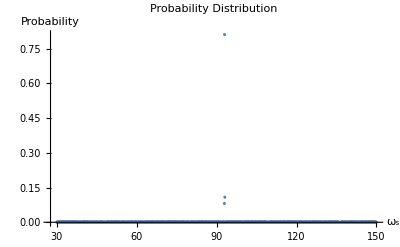

```mathematica
data2 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data2,PlotRange->All,PlotLabel->"Probability Distribution",AxesLabel->{"ω_s","Probability"}]
```

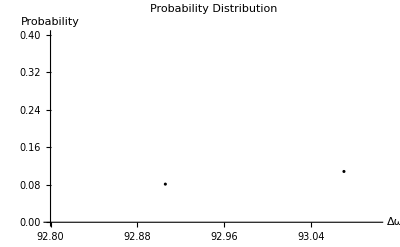

```mathematica
data4 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data4,PlotRange->{{92.8,93.1},{0,0.40}},PlotStyle->{Black},PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

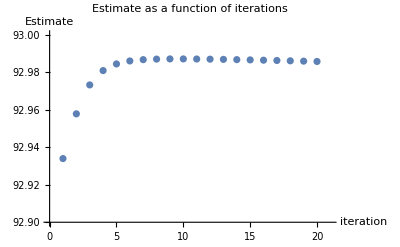

```mathematica
data3 = Table[{i,Meanlist[[i]]},{i,1,Length[Meanlist]}];
ListPlot[data3,PlotRange->{{0,21},{92.90,93.0}},PlotLabel->"Estimate as a function of iterations",AxesLabel->{"iteration","Estimate"}]
```

Estimate and Standard Deviation

```mathematica
Estimate1 = Meanlist[[-1]]
```

92.9857+7.53085×10^-18 ⅈ

```mathematica
std=Sqrt[COV[X,Ω]]
```

0.0360992+3.51039×10^-18 ⅈ

### Flat Gaussian Prior

```mathematica
ωleft= 30;
ωright = 150;
np = 2000;
Prior = NormalDistribution[(ωleft+ωright)/2,(ωright-ωleft)/3];
X = RandomVariate[Prior,np];
Ω = Table[1/np,{i,1,np}];
a=0.98;
resampthreshold=0.6;
Meanlist={};
IMPLEMENT[data1,Ω,X,a,resampthreshold,Meanlist,20]
```

General::munfl: (1.01863×10^-159+5.42423×10^-175 ⅈ) (1.13939×10^-160+6.05493×10^-176 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.51902×10^-147+5.30397×10^-163 ⅈ) (5.05473×10^-148+5.87812×10^-164 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.86266×10^-105+2.68525×10^-120 ⅈ) (3.74816×10^-210+4.10588×10^-225 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
AbsolutePercentError=Abs[(Meanlist[[-1]]-ωs)/ωs]*100
```

0.000747351

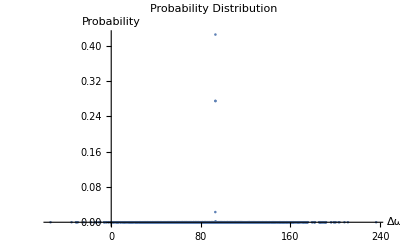

```mathematica
data2 = Table[{X[[i]],Ω[[i]]},{i,1,Length[X]}];
ListPlot[data2,PlotRange->All,PlotLabel->"Probability Distribution",AxesLabel->{"Δω","Probability"}]
```

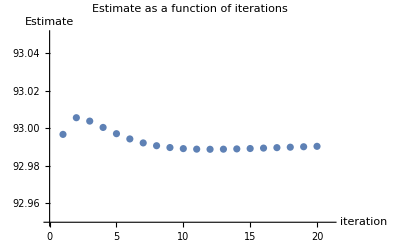

```mathematica
data3 = Table[{i,Meanlist[[i]]},{i,1,Length[Meanlist]}];
ListPlot[data3,PlotRange->{{0,21},{92.95,93.05}},PlotLabel->"Estimate as a function of iterations",AxesLabel->{"iteration","Estimate"}]
```

```mathematica
Estimate2 = Meanlist[[-1]]
```

92.9904+1.12076×10^-17 ⅈ